# Telaio simmetrico con carico trasversale distribuito

## Analisi elastica

```mathematica
ClearAll["Global`*"];

l1=l;
l2=2*l;
EJ1 = EJ;
EJ2=8*EJ;

v1[s1_]=c1+c2*s1+c3*s1^2+c4*s1^3;
v2[s2_]=c5+c6*s2+c7*s2^2+c8*s2^3+q0/(24*EJ2)*s2^4;
v3[s3_]=c9+c10*s3+c11*s3^2+c12*s3^3;

eqlin = {
v1[0]==0, 
v1'[0]==0, 
v2[0]==0, 
v1'[l1]==v2'[0],
-EJ1*v1''[l1]==-EJ2*v2''[0],
v1[l1]==-v3[0],
-EJ1*(v1'''[l1]+0)==-N2,
-EJ2*(v2'''[0]+0)==N1,
v2[l2]==0,
v2'[l2]==v3'[0],
-EJ2*v2''[l2]==-EJ1*v3''[0],
-EJ2*(v2'''[l2]+0)==-1*N3,
-EJ1*(v3'''[0]+0)==1*N2,
v3[l1]==0,
v3'[l1]==0
};
inclin = {c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12, N1, N2, N3};

{bb, ML}=CoefficientArrays[
eqlin,
inclin
]//Normal;
bb= -bb;
MatrixForm[ML]
MatrixForm[bb]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 l | 3 l^2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 EJ | -6 EJ l | 0 | 0 | 16 EJ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | l | l^2 | l^3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -6 EJ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -48 EJ | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 l | 4 l^2 | 8 l^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 4 l | 12 l^2 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -16 EJ | -96 EJ l | 0 | 0 | 2 EJ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -48 EJ | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 EJ | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | l | l^2 | l^3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 l | 3 l^2 | 0 | 0 | 0)

(0
0
0
0
0
0
0
0
-(l^4 q0)/(12 EJ)
-(l^3 q0)/(6 EJ)
2 l^2 q0
2 l q0
0
0
0)

```mathematica
Det[ML]
```

-115200 EJ^3 l^7

```mathematica
linsol = Solve[eqlin, inclin][[1]]
```

{c1→0,c2→0,c3→-(l^2 q0)/(36 EJ),c4→(l q0)/(36 EJ),c5→0,c6→(l^3 q0)/(36 EJ),c7→(l^2 q0)/(144 EJ),c8→-(l q0)/(48 EJ),c9→0,c10→-(l^3 q0)/(36 EJ),c11→(l^2 q0)/(18 EJ),c12→-(l q0)/(36 EJ),N1→l q0,N2→(l q0)/6,N3→l q0}

```mathematica
{v1lin[s1_,q0_], v2lin[s2_,q0_], v3lin[s3_,q0_]}= {v1[s1], v2[s2], v3[s3]}/.linsol
```

{-(l^2 q0 s1^2)/(36 EJ)+(l q0 s1^3)/(36 EJ),(l^3 q0 s2)/(36 EJ)+(l^2 q0 s2^2)/(144 EJ)-(l q0 s2^3)/(48 EJ)+(q0 s2^4)/(192 EJ),-(l^3 q0 s3)/(36 EJ)+(l^2 q0 s3^2)/(18 EJ)-(l q0 s3^3)/(36 EJ)}

```mathematica
{N1lin[q0_], N2lin[q0_], N3lin[q0_]} = {N1, N2, N3}/.linsol
```

{l q0,(l q0)/6,l q0}

```mathematica
θB[q0_] = D[v1lin[s1, q0], s1]/.s1->l1
θB[q0] == D[v2lin[s2, q0], s2]/.s2->0
```

(l^3 q0)/(36 EJ)

True

## Verifiche

```mathematica
eqlin/.linsol
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## Plot

```mathematica
ClearAll[l, EJ, q0, def, undef, frame, gr, comb, tab]
l = 1;
EJ=1;
q0fin = 20;

undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1}, {s2, 0, l2}],
ParametricPlot[{l2, s3}, {s3, 0, l1}]
}/.Directive[__]->Gray,
PlotRange->Full
];

def[q0_] := Show[
{
ParametricPlot[{v1lin[s1, q0], s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1-v2lin[s2, q0]}, {s2, 0, l2}],
ParametricPlot[{l2-v3lin[s3, q0], l1-s3}, {s3, 0, l1}]
}/.Directive[__]->Thick,
PlotRange->Full
];

frame[q0_]:= Show[{undef, def[q0]}, ImageSize->500];

gr[q0_]:=Show[{ParametricPlot[{θB[q], q}, {q, 0, 20},
AspectRatio->1/GoldenRatio,
PlotRangePadding->None,
PlotRangeClipping->True],
Graphics[{PointSize[Large],Red,Point[{θB[q0],q0}]}]
},
Axes->False, 
Frame->True, 
ImageSize->500
];

comb[q0_]:= Grid[{{frame[q0], gr[q0]}}, Spacings->0];

tab = Table[comb[q0], {q0, 0., q0fin, .5}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->Infinity, 
DefaultDuration->5
]

ClearAll[EJ, l, q0];
```

## Analisi del II ordine

## Soluzione generale

```mathematica
ClearAll[l, l1, l2, EJ, EJ1, EJ2, c1,c2,c3, c4,c5,c6,c7,c8,c9,c10,c11,c12,q0, α1, α2, α3, α1sq, α2sq, α3sq, s1, s2,s3, v1, v2,v3, eqnl, incnl, RR, MM];

l1=l;
l2=2*l;
EJ1 = EJ;
EJ2=8*EJ;


v1[s1_]=c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_]=c5+c6*s2+c7*Cos[α2*s2]+c8*Sin[α2*s2]+q0/(2*EJ2*α2^2)*s2^2;
v3[s3_]=c9+c10*s3+c11*Cos[α3*s3]+c12*Sin[α3*s3];

(*
Subscript[α, i] sq = Subscript[α, i]^2
*)

eqnl = {
v1[0]==0, 
v1'[0]==0, 
v1'[l1]==v2'[0],
-v1''[l1]==-EJ2/EJ1*v2''[0],
-(v1'''[l1]+α1^2*v1'[l1])==-EJ2/EJ1*α2sq,
-(v2'''[0]+α2^2*v2'[0])==EJ1/EJ2*α1sq,
v2'[l2]==v3'[0],
-EJ2*v2''[l2]==-EJ1*v3''[0],
-(v3'''[0]+α3^2*v3'[0])==EJ2/EJ1*α2sq,
-(v2'''[l2]+α2^2*v2'[l2])==-EJ1/EJ2*α3sq,
v3[l1]==0,
v3'[l1]==0,
v2[0]==0, 
v2[l2]==0,
v1[l1]==-v3[0]
};
incnl = {c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12, α1sq, α2sq, α3sq};

{RR, MM} = CoefficientArrays[
eqnl,incnl
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | α1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -α1 Sin[l α1] | α1 Cos[l α1] | 0 | -1 | 0 | -α2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | α1^2 Cos[l α1] | α1^2 Sin[l α1] | 0 | 0 | -8 α2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -α1^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | -α2^2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -α2 Sin[2 l α2] | α2 Cos[2 l α2] | 0 | -1 | 0 | -α3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8 EJ α2^2 Cos[2 l α2] | 8 EJ α2^2 Sin[2 l α2] | 0 | 0 | -EJ α3^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α3^2 | 0 | 0 | 0 | -8 | 0
0 | 0 | 0 | 0 | 0 | -α2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | l | Cos[l α3] | Sin[l α3] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -α3 Sin[l α3] | α3 Cos[l α3] | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 l | Cos[2 l α2] | Sin[2 l α2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | l | Cos[l α1] | Sin[l α1] | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0)

(0
0
0
-q0/(EJ α2^2)
0
0
-(l q0)/(4 EJ α2^2)
q0/α2^2
0
(l q0)/(4 EJ)
0
0
0
-(l^2 q0)/(4 EJ α2^2)
0)

## Soluzione con azioni assiali lineari

### Soluzione generale

```mathematica
ClearAll[l, l1, l2, EJ, EJ1, EJ2, c1,c2,c3, c4,c5,c6,c7,c8,c9,c10,c11,c12,q0, α1, α2, α3, α1sq, α2sq, α3sq, s1, s2,s3, v1, v2,v3, incnl, RR, MM];

α1 =Sqrt[(N1/.linsol)/EJ];
α2 =Sqrt[(N2/.linsol)/EJ2];
α3=Sqrt[(N3/.linsol)/EJ1];

{α1sq, α2sq, α3sq} = {α1^2, α2^2, α3^2};

l1=l;
l2=2*l;
EJ1 = EJ;
EJ2=8*EJ;


v1[s1_]=c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_]=c5+c6*s2+c7*Cos[α2*s2]+c8*Sin[α2*s2]+q0/(2*EJ2*α2^2)*s2^2;
v3[s3_]=c9+c10*s3+c11*Cos[α3*s3]+c12*Sin[α3*s3];

(*
Subscript[α, i] sq = Subscript[α, i]^2
*)
eqnl = {
v1[0]==0, 
v1'[0]==0, 
v1'[l1]==v2'[0],
-v1''[l1]==-EJ2/EJ1*v2''[0],
(*-(v1'''[l1]+α1^2*v1'[l1])==-EJ2/EJ1*α2sq, QUA SI SOTTRAE LA (9)*)
(*-(v2'''[0]+α2^2*v2'[0])==EJ1/EJ2*α1sq, VA ELIMINATA*)
-(v1'''[l1]+α1^2*v1'[l1])+EJ2/EJ1*α2sq-(v3'''[0]+α3^2*v3'[0])-EJ2/EJ1*α2sq==0,
v2'[l2]==v3'[0],
-EJ2*v2''[l2]==-EJ1*v3''[0],
(*-(v3'''[0]+α3^2*v3'[0])==EJ2/EJ1*α2sq, VA SOTTRATTA ALLA (5)*)
(*-(v2'''[l2]+α2^2*v2'[l2])==-EJ1/EJ2*α3sq, VA ELIMINATA*)
v3[l1]==0,
v3'[l1]==0,
v2[0]==0, 
v2[l2]==0,
v1[l1]==-v3[0]
};

incnl = {c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12};

{RR, MM} = CoefficientArrays[
eqnl,incnl
]//Simplify//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | √((l q0)/EJ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -√((l q0)/EJ) Sin[l √((l q0)/EJ)] | √((l q0)/EJ) Cos[l √((l q0)/EJ)] | 0 | -1 | 0 | -(√((l q0)/EJ))/(4 √3) | 0 | 0 | 0 | 0
0 | 0 | (l q0 Cos[l √((l q0)/EJ)])/EJ | (l q0 Sin[l √((l q0)/EJ)])/EJ | 0 | 0 | -(l q0)/(6 EJ) | 0 | 0 | 0 | 0 | 0
0 | -(l q0)/EJ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(l q0)/EJ | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -(√((l q0)/EJ) Sin[(l √((l q0)/EJ))/(2 √3)])/(4 √3) | (√((l q0)/EJ) Cos[(l √((l q0)/EJ))/(2 √3)])/(4 √3) | 0 | -1 | 0 | -√((l q0)/EJ)
0 | 0 | 0 | 0 | 0 | 0 | 1/6 l q0 Cos[(l √((l q0)/EJ))/(2 √3)] | 1/6 l q0 Sin[(l √((l q0)/EJ))/(2 √3)] | 0 | 0 | -l q0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | l | Cos[l √((l q0)/EJ)] | Sin[l √((l q0)/EJ)]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -√((l q0)/EJ) Sin[l √((l q0)/EJ)] | √((l q0)/EJ) Cos[l √((l q0)/EJ)]
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 l | Cos[(l √((l q0)/EJ))/(2 √3)] | Sin[(l √((l q0)/EJ))/(2 √3)] | 0 | 0 | 0 | 0
1 | l | Cos[l √((l q0)/EJ)] | Sin[l √((l q0)/EJ)] | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

(0
0
0
-48/l
0
-12
(48 EJ)/l
0
0
0
-12 l
0)

```mathematica
l = 1;
EJ= 1;

nlsol = Solve[eqnl, incnl][[1]];//AbsoluteTiming
nlsol
```

{11.9376,Null}

{c1→-((12 Sec[√q0] (24 √3+√3 q0-48 √3 Cos[(√q0)/(2 √3)]+√3 q0 Cos[(√q0)/(2 √3)]+24 √3 1^2-1+24 √3 Sin[(√q0)/1]^2+8 √3 √q0 Tan[√q0]-8 √3 √q0 Cos[(√q0)/(2 √3)] Tan[√q0]-2 q0 Sin[(√q0)/(2 √3)] Tan[√q0]))/(q0 (-6 √3+12 √3 Cos[(√q0)/(2 √3)]-6 √3 Cos[(√q0)/(2 √3)]^2+3 √q0 Sin[(√q0)/(2 √3)]-6 √3 1^2+4 √3 √q0 Cos[(√q0)/(2 √3)] Tan[√q0]-24 Sin[(√q0)/(2 √3)] Tan[√q0]-4 √q0 Sin[(√q0)/(2 √3)] Tan[√q0]^2)))+(√q0 1 (1))/1,c2→-1,9,c12→1}
 |  |  |  |

```mathematica
l=1;
EJ=1;
q0=10;

Simplify[eqnl[[1]]/.nlsol]
Simplify[eqnl[[2]]/.nlsol]
(*Simplify[eqnl[[4]]/.nlsol]*)
```

True

True

#### Plot

```mathematica
ClearAll[l, EJ, q0, def, undef, frame, gr, comb, tab]

v1nl[s1_, q0_] = v1[s1]/.nlsol;
v2nl[s2_, q0_] = v2[s2]/.nlsol;
v3nl[s3_, q0_] = v3[s3]/.nlsol;

l=1;
EJ=1;
q0fin = 30.73;


θBnl[q0_] =Derivative[1, 0][v1nl][l1, q0];

undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1}, {s2, 0, l2}],
ParametricPlot[{l2, s3}, {s3, 0, l1}]
}/.Directive[__]->Gray,
PlotRange->Full
];

def[q0_] := Show[
{
ParametricPlot[{v1nl[s1, q0], s1}, {s1, 0, l1}, PlotStyle->Thick],
ParametricPlot[{s2, l1-v2nl[s2, q0]}, {s2, 0, l2}, PlotStyle->Thick],
ParametricPlot[{l2-v3nl[s3, q0], l1-s3}, {s3, 0, l1}, PlotStyle->Thick],
ParametricPlot[{v1lin[s1, q0], s1}, {s1, 0, l1}, PlotStyle->{Gray, Dashed}],
ParametricPlot[{s2, l1-v2lin[s2, q0]}, {s2, 0, l2},PlotStyle->{Gray, Dashed}],
ParametricPlot[{l2-v3lin[s3, q0], l1-s3}, {s3, 0, l1},PlotStyle->{Gray, Dashed}]
},
PlotRange->Full
];

frame[q0_]:= Show[{undef, def[q0]}, ImageSize->500];


gr[q0_]:=Show[
{
ParametricPlot[{θBnl[q], q}, {q, 0.1, q0fin}],
ParametricPlot[{θB[q], q}, {q, .1, q0fin}, PlotStyle->{Gray, Dashed}],
Graphics[{PointSize[Large],Gray,Point[{θB[q0],q0}]}],
Graphics[{PointSize[Large],Red,Point[{θBnl[q0],q0}]}]
}, 
PlotRange->{{0, 20}, {0,q0fin }},
AspectRatio->1/GoldenRatio,
Axes->False,
Frame->True,
FrameLabel->{"θ_B", "q_0/EJ"},
ImageSize->500, 
LabelStyle->18
];


comb[q0_]:= Grid[{{frame[q0], gr[q0]}}, Spacings->0];

tab = Table[comb[q0], {q0, 0.1, q0fin, 1}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->1, 
DefaultDuration->10
]
```

### Primo carico e modo critico (anti-simmetrico)

```mathematica
ClearAll[l ,EJ, c1, c2, c3,c4,c5,c6,c7,c8,c9,c10,c11,c12, c1cr, q0, q0cr];

l = 1;
EJ=1;

MM//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | √q0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -√q0 Sin[√q0] | √q0 Cos[√q0] | 0 | -1 | 0 | -(√q0)/(4 √3) | 0 | 0 | 0 | 0
0 | 0 | q0 Cos[√q0] | q0 Sin[√q0] | 0 | 0 | -q0/6 | 0 | 0 | 0 | 0 | 0
0 | -q0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -q0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -(√q0 Sin[(√q0)/(2 √3)])/(4 √3) | (√q0 Cos[(√q0)/(2 √3)])/(4 √3) | 0 | -1 | 0 | -√q0
0 | 0 | 0 | 0 | 0 | 0 | 1/6 q0 Cos[(√q0)/(2 √3)] | 1/6 q0 Sin[(√q0)/(2 √3)] | 0 | 0 | -q0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | Cos[√q0] | Sin[√q0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -√q0 Sin[√q0] | √q0 Cos[√q0]
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | Cos[(√q0)/(2 √3)] | Sin[(√q0)/(2 √3)] | 0 | 0 | 0 | 0
1 | 1 | Cos[√q0] | Sin[√q0] | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

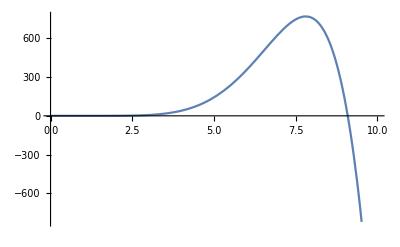

```mathematica
detMM[q0_] = Det[MM];

Plot[detMM[q0], {q0, 0, 10}]
```

```mathematica
q0cr = q0/.FindRoot[detMM[q0] == 0, {q0, 9}]
```

9.09041

```mathematica
MMcr = MM/.q0->q0cr;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3.01503 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -0.380569 | -2.99092 | 0 | -1 | 0 | -0.435182 | 0 | 0 | 0 | 0
0 | 0 | -9.01771 | 1.14743 | 0 | 0 | -1.51507 | 0 | 0 | 0 | 0 | 0
0 | -9.09041 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.09041 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -0.332725 | 0.280496 | 0 | -1 | 0 | -3.01503
0 | 0 | 0 | 0 | 0 | 0 | 0.976534 | 1.15837 | 0 | 0 | -9.09041 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -0.992002 | 0.126224
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -0.380569 | -2.99092
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 0.644548 | 0.764564 | 0 | 0 | 0 | 0
1 | 1 | -0.992002 | 0.126224 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
MMRR = Transpose[Append[Transpose[MMcr], RR]];
MatrixForm[MMRR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3.01503 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -0.380569 | -2.99092 | 0 | -1 | 0 | -0.435182 | 0 | 0 | 0 | 0 | 0
0 | 0 | -9.01771 | 1.14743 | 0 | 0 | -1.51507 | 0 | 0 | 0 | 0 | 0 | -48
0 | -9.09041 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.09041 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -0.332725 | 0.280496 | 0 | -1 | 0 | -3.01503 | -12
0 | 0 | 0 | 0 | 0 | 0 | 0.976534 | 1.15837 | 0 | 0 | -9.09041 | 0 | 48
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -0.992002 | 0.126224 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -0.380569 | -2.99092 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 0.644548 | 0.764564 | 0 | 0 | 0 | 0 | -12
1 | 1 | -0.992002 | 0.126224 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

```mathematica
MatrixRank[MMcr]
MatrixRank[MMRR]
```

11

11

```mathematica
Length[incnl]
```

12

```mathematica
ClearAll[EJ, l];
EJ=1;
l=1;

nlAsol=Solve[eqnl/.q0->q0cr, incnl][[1]]//Chop
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{c2→0.168038,c3→-1. c1,c4→-0.0557334,c5→-31.6395-5.95201 c1,c6→-5.51893+5.95201 c1,c7→31.6395+5.95201 c1,c8→13.4511-12.8025 c1,c9→0.00638843-1. c1,c10→-0.168038,c11→-0.167392-0.992002 c1,c12→-0.0348836+0.126224 c1}

```mathematica
c1cr = c1/.Solve[(v1[l1]/.nlAsol/.q0->q0cr)==0, c1][[1]]
```

-0.0808248

#### Plot

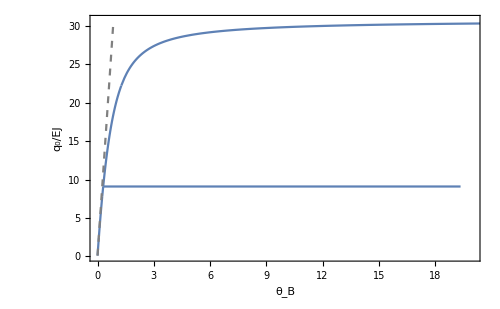

```mathematica
v1nlA[s1_, c1_] = v1[s1]/.nlAsol;
v2nlA[s2_, c1_] = v2[s2]/.nlAsol;
v3nlA[s3_, c1_] = v3[s3]/.nlAsol;


θBnlA[c1_] = Derivative[1, 0][v1nlA][l1, c1]/.q0->q0cr;


Show[
{
ParametricPlot[{θBnl[q], q}, {q, 0.1, q0fin}],
ParametricPlot[{θB[q], q}, {q, .1, q0fin}, PlotStyle->{Gray, Dashed}],
ParametricPlot[{θBnlA[c1], q0cr}, {c1, c1cr, 50}]
}, 
PlotRange->{{0, 20}, {0,q0fin }},
AspectRatio->1/GoldenRatio,
Axes->False,
Frame->True,
FrameLabel->{"θ_B", "q_0/EJ"},
ImageSize->500, 
LabelStyle->18
]
```

```mathematica
undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1}, {s2, 0, l2}],
ParametricPlot[{l2, s3}, {s3, 0, l1}]
}/.Directive[__]->Gray,
PlotRange->Full
];

def[c1_] := Show[
{
ParametricPlot[{v1nlA[s1, c1]/.q0->q0cr, s1}, {s1, 0, l1}, PlotStyle->Thick],
ParametricPlot[{v1nlA[l1, c1]+s2/.q0->q0cr, l1-v2nlA[s2, c1]/.q0->q0cr}, {s2, 0, l2}, PlotStyle->Thick],
ParametricPlot[{l2-v3nlA[s3, c1]/.q0->q0cr, l1-s3}, {s3, 0, l1}, PlotStyle->Thick]
},
PlotRange->Full
];

frame[c1_]:= Show[{undef, def[c1]}, ImageSize->500];


gr[c1_]:=Show[
{
ParametricPlot[{θBnlA[c], q0cr}, {c, c1cr, q0fin}],
ParametricPlot[{θBnl[q], q}, {q, 0.1, q0fin}],
ParametricPlot[{θB[q], q}, {q, .1, q0fin}, PlotStyle->Directive[{Gray, Dashed}]],
Graphics[{PointSize[Large],Red,Point[{θBnlA[c1],q0cr}]}]
}, 
PlotRange->{{0, 1}, {0,q0fin }},
AspectRatio->1/GoldenRatio,
Axes->False,
Frame->True,
FrameLabel->{"θ_B", "q_0/EJ"},
ImageSize->500, 
LabelStyle->18
];


comb[c1_]:= Grid[{{frame[c1], gr[c1]}}, Spacings->0];

tab = Table[comb[c1], {c1, c1cr, .5, .01}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->1, 
DefaultDuration->10
]
```

### Secondo carico e modo critico (simmetrico)

```mathematica
ClearAll[c1, c2, c3, c4,c5,c6,c7,c8,c9,c10,c11,c12, q0cr, c1cr, MMcr, MMRR, l, EJ];

l = 1;
EJ=1;

MM//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | √q0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -√q0 Sin[√q0] | √q0 Cos[√q0] | 0 | -1 | 0 | -(√q0)/(4 √3) | 0 | 0 | 0 | 0
0 | 0 | q0 Cos[√q0] | q0 Sin[√q0] | 0 | 0 | -q0/6 | 0 | 0 | 0 | 0 | 0
0 | -q0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -q0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -(√q0 Sin[(√q0)/(2 √3)])/(4 √3) | (√q0 Cos[(√q0)/(2 √3)])/(4 √3) | 0 | -1 | 0 | -√q0
0 | 0 | 0 | 0 | 0 | 0 | 1/6 q0 Cos[(√q0)/(2 √3)] | 1/6 q0 Sin[(√q0)/(2 √3)] | 0 | 0 | -q0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | Cos[√q0] | Sin[√q0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -√q0 Sin[√q0] | √q0 Cos[√q0]
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | Cos[(√q0)/(2 √3)] | Sin[(√q0)/(2 √3)] | 0 | 0 | 0 | 0
1 | 1 | Cos[√q0] | Sin[√q0] | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

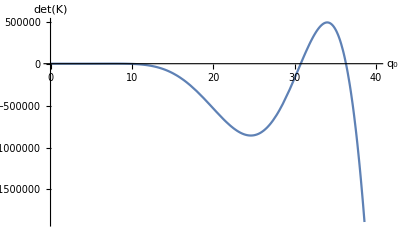

```mathematica
detMM[q0_] = Det[MM];

Plot[detMM[q0], {q0, 0, 40}, AxesLabel->{"q_0", "det(K)"}]
```

```mathematica
q0cr = q0/.FindRoot[detMM[q0] == 0, {q0, 30}]
```

30.7372

```mathematica
MMcr = MM/.q0->q0cr;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 5.54411 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3.73454 | 4.0976 | 0 | -1 | 0 | -0.800223 | 0 | 0 | 0 | 0
0 | 0 | 22.7176 | -20.7047 | 0 | 0 | -5.12286 | 0 | 0 | 0 | 0 | 0
0 | -30.7372 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -30.7372 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -0.799872 | -0.0237234 | 0 | -1 | 0 | -5.54411
0 | 0 | 0 | 0 | 0 | 0 | -0.151872 | 5.12061 | 0 | 0 | -30.7372 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0.739092 | -0.673605
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3.73454 | 4.0976
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | -0.029646 | 0.99956 | 0 | 0 | 0 | 0
1 | 1 | 0.739092 | -0.673605 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
MMRR = Transpose[Append[Transpose[MMcr], RR]];
MatrixForm[MMRR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 5.54411 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3.73454 | 4.0976 | 0 | -1 | 0 | -0.800223 | 0 | 0 | 0 | 0 | 0
0 | 0 | 22.7176 | -20.7047 | 0 | 0 | -5.12286 | 0 | 0 | 0 | 0 | 0 | -48
0 | -30.7372 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -30.7372 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -0.799872 | -0.0237234 | 0 | -1 | 0 | -5.54411 | -12
0 | 0 | 0 | 0 | 0 | 0 | -0.151872 | 5.12061 | 0 | 0 | -30.7372 | 0 | 48
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0.739092 | -0.673605 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3.73454 | 4.0976 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | -0.029646 | 0.99956 | 0 | 0 | 0 | 0 | -12
1 | 1 | 0.739092 | -0.673605 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

```mathematica
MatrixRank[MMcr]
MatrixRank[MMRR]
```

11

12

```mathematica
(*
IL SISTEMA NON AMMETTE SOLUZIONI -> INSTABILITÀ PER DIVERGENZA
*)

ClearAll[EJ, l];
EJ=1;
l=1;

nlSsol=Solve[eqnl/.q0->q0cr, incnl]//Chop
```

{}

#### Plot

```mathematica
ClearAll[l, EJ, q0, def, undef, frame, gr, comb, tab]

v1nl[s1_, q0_] = v1[s1]/.nlsol;
v2nl[s2_, q0_] = v2[s2]/.nlsol;
v3nl[s3_, q0_] = v3[s3]/.nlsol;

l=1;
EJ=1;
q0fin = 30.73;


θBnl[q0_] =Derivative[1, 0][v1nl][l1, q0];

undef = Show[
{
ParametricPlot[{0, s1}, {s1, 0, l1}],
ParametricPlot[{s2, l1}, {s2, 0, l2}],
ParametricPlot[{l2, s3}, {s3, 0, l1}]
}/.Directive[__]->Gray,
PlotRange->Full
];

def[q0_] := Show[
{
ParametricPlot[{v1nl[s1, q0], s1}, {s1, 0, l1}, PlotStyle->Thick],
ParametricPlot[{s2, l1-v2nl[s2, q0]}, {s2, 0, l2}, PlotStyle->Thick],
ParametricPlot[{l2-v3nl[s3, q0], l1-s3}, {s3, 0, l1}, PlotStyle->Thick],
ParametricPlot[{v1lin[s1, q0], s1}, {s1, 0, l1}, PlotStyle->{Gray, Dashed}],
ParametricPlot[{s2, l1-v2lin[s2, q0]}, {s2, 0, l2},PlotStyle->{Gray, Dashed}],
ParametricPlot[{l2-v3lin[s3, q0], l1-s3}, {s3, 0, l1},PlotStyle->{Gray, Dashed}]
},
PlotRange->Full
];

frame[q0_]:= Show[{undef, def[q0]}, ImageSize->500];


gr[q0_]:=Show[
{
ParametricPlot[{θBnl[q], q}, {q, 0.1, q0fin}],
ParametricPlot[{θB[q], q}, {q, .1, q0fin}, PlotStyle->{Gray, Dashed}],
Graphics[{PointSize[Large],Gray,Point[{θB[q0],q0}]}],
Graphics[{PointSize[Large],Red,Point[{θBnl[q0],q0}]}]
}, 
PlotRange->{{0, 20}, {0,q0fin }},
AspectRatio->1/GoldenRatio,
Axes->False,
Frame->True,
FrameLabel->{"θ_B", "q_0/EJ"},
ImageSize->500, 
LabelStyle->18
];


comb[q0_]:= Grid[{{frame[q0], gr[q0]}}, Spacings->0];

tab = Table[comb[q0], {q0, 0.1, q0fin, 1}];
ListAnimate[
tab, 
AnimationRunning->False,
AnimationRepetitions->1, 
DefaultDuration->10
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Hyperlink["Press here to show plots", {EvaluationNotebook[], "divergence_plot"}]
```

Press here to show plots2c8d62c6-43d7-4e3b-94b6-297a03da2befdivergence_plotButtonData

## Soluzione con azioni assiali non lineari

### Soluzione generale

```mathematica
ClearAll[l, l1, l2, EJ, EJ1, EJ2, c1,c2,c3, c4,c5,c6,c7,c8,c9,c10,c11,c12,q0, α1, α2, α3, α1sq, α2sq, α3sq, s1, s2,s3, v1, v2,v3, incnl, RR, MM, eqnl];

{α1sq, α2sq, α3sq} = {α1^2, α2^2, α3^2};

l1=l;
l2=2*l;
EJ1 = EJ;
EJ2=8*EJ;


v1[s1_]=c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_]=c5+c6*s2+c7*Cos[α2*s2]+c8*Sin[α2*s2]+q0/(2*EJ2*α2^2)*s2^2;
v3[s3_]=c9+c10*s3+c11*Cos[α3*s3]+c12*Sin[α3*s3];

(*
Subscript[α, i] sq = Subscript[α, i]^2
*)

eqnl[q0_] = {
v1[0]==0, 
v1'[0]==0, 
v1'[l1]==v2'[0],
-v1''[l1]==-EJ2/EJ1*v2''[0],
-(v1'''[l1]+α1^2*v1'[l1])==-EJ2/EJ1*α2sq,
-(v2'''[0]+α2^2*v2'[0])==EJ1/EJ2*α1sq,
v2'[l2]==v3'[0],
-EJ2*v2''[l2]==-EJ1*v3''[0],
-(v3'''[0]+α3^2*v3'[0])==EJ2/EJ1*α2sq,
-(v2'''[l2]+α2^2*v2'[l2])==-EJ1/EJ2*α3sq, 
v3[l1]==0,
v3'[l1]==0,
v2[0]==0, 
v2[l2]==0,
v1[l1]==-v3[0]
};

F = 
{
v1[0], 
v1'[0], 
v1'[l1]-v2'[0],
-v1''[l1]+EJ2/EJ1*v2''[0],
-(v1'''[l1]+α1^2*v1'[l1])+EJ2/EJ1*α2sq,
-(v2'''[0]+α2^2*v2'[0])-EJ1/EJ2*α1sq,
v2'[l2]-v3'[0],
-EJ2*v2''[l2]+EJ1*v3''[0],
-(v3'''[0]+α3^2*v3'[0])-EJ2/EJ1*α2sq,
-(v2'''[l2]+α2^2*v2'[l2])+EJ1/EJ2*α3sq, 
v3[l1],
v3'[l1],
v2[0], 
v2[l2],
v1[l1]+v3[0]
};

incnl = {c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12, α1, α2, α3};


TableForm[F]//Simplify
```

c1+c3
c2+c4 α1
c2-c6-c8 α2+c4 α1 Cos[l α1]-c3 α1 Sin[l α1]
q0/(EJ α2^2)-8 c7 α2^2+c3 α1^2 Cos[l α1]+c4 α1^2 Sin[l α1]
-c2 α1^2+8 α2^2
-α1^2/8-c6 α2^2
-c10+c6+(l q0)/(4 EJ α2^2)-c12 α3+c8 α2 Cos[2 l α2]-c7 α2 Sin[2 l α2]
-q0/α2^2-c11 EJ α3^2+8 c7 EJ α2^2 Cos[2 l α2]+8 c8 EJ α2^2 Sin[2 l α2]
-8 α2^2-c10 α3^2
1/8 (-(2 l q0)/EJ-8 c6 α2^2+α3^2)
c9+c10 l+c11 Cos[l α3]+c12 Sin[l α3]
c10+c12 α3 Cos[l α3]-c11 α3 Sin[l α3]
c5+c7
c5+2 c6 l+(l^2 q0)/(4 EJ α2^2)+c7 Cos[2 l α2]+c8 Sin[2 l α2]
c1+c11+c9+c2 l+c3 Cos[l α1]+c4 Sin[l α1]

```mathematica
J = D[F, {incnl}];
MatrixForm[J]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | α1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | c4 | 0 | 0
0 | 1 | -α1 Sin[l α1] | α1 Cos[l α1] | 0 | -1 | 0 | -α2 | 0 | 0 | 0 | 0 | c4 Cos[l α1]-c3 l α1 Cos[l α1]-c3 Sin[l α1]-c4 l α1 Sin[l α1] | -c8 | 0
0 | 0 | α1^2 Cos[l α1] | α1^2 Sin[l α1] | 0 | 0 | -8 α2^2 | 0 | 0 | 0 | 0 | 0 | 2 c3 α1 Cos[l α1]+c4 l α1^2 Cos[l α1]+2 c4 α1 Sin[l α1]-c3 l α1^2 Sin[l α1] | 8 (-q0/(4 EJ α2^3)-2 c7 α2) | 0
0 | -α1^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 c4 α1^2 Cos[l α1]-c3 l α1^3 Cos[l α1]-3 c3 α1^2 Sin[l α1]-c4 l α1^3 Sin[l α1]-2 α1 (c2+c4 α1 Cos[l α1]-c3 α1 Sin[l α1])-α1^2 (c4 Cos[l α1]-c3 l α1 Cos[l α1]-c3 Sin[l α1]-c4 l α1 Sin[l α1]) | 16 α2 | 0
0 | 0 | 0 | 0 | 0 | -α2^2 | 0 | 0 | 0 | 0 | 0 | 0 | -α1/4 | 2 c8 α2^2-2 α2 (c6+c8 α2) | 0
0 | 0 | 0 | 0 | 0 | 1 | -α2 Sin[2 l α2] | α2 Cos[2 l α2] | 0 | -1 | 0 | -α3 | 0 | -(l q0)/(2 EJ α2^3)+c8 Cos[2 l α2]-2 c7 l α2 Cos[2 l α2]-c7 Sin[2 l α2]-2 c8 l α2 Sin[2 l α2] | -c12
0 | 0 | 0 | 0 | 0 | 0 | 8 EJ α2^2 Cos[2 l α2] | 8 EJ α2^2 Sin[2 l α2] | 0 | 0 | -EJ α3^2 | 0 | 0 | -8 EJ (-q0/(4 EJ α2^3)-2 c7 α2 Cos[2 l α2]-2 c8 l α2^2 Cos[2 l α2]-2 c8 α2 Sin[2 l α2]+2 c7 l α2^2 Sin[2 l α2]) | -2 c11 EJ α3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α3^2 | 0 | 0 | 0 | -16 α2 | 2 c12 α3^2-2 α3 (c10+c12 α3)
0 | 0 | 0 | 0 | 0 | -α2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 c8 α2^2 Cos[2 l α2]-2 c7 l α2^3 Cos[2 l α2]-3 c7 α2^2 Sin[2 l α2]-2 c8 l α2^3 Sin[2 l α2]-2 α2 (c6+(l q0)/(4 EJ α2^2)+c8 α2 Cos[2 l α2]-c7 α2 Sin[2 l α2])-α2^2 (-(l q0)/(2 EJ α2^3)+c8 Cos[2 l α2]-2 c7 l α2 Cos[2 l α2]-c7 Sin[2 l α2]-2 c8 l α2 Sin[2 l α2]) | α3/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | l | Cos[l α3] | Sin[l α3] | 0 | 0 | c12 l Cos[l α3]-c11 l Sin[l α3]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -α3 Sin[l α3] | α3 Cos[l α3] | 0 | 0 | c12 Cos[l α3]-c11 l α3 Cos[l α3]-c11 Sin[l α3]-c12 l α3 Sin[l α3]
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 l | Cos[2 l α2] | Sin[2 l α2] | 0 | 0 | 0 | 0 | 0 | -(l^2 q0)/(2 EJ α2^3)+2 c8 l Cos[2 l α2]-2 c7 l Sin[2 l α2] | 0
1 | l | Cos[l α1] | Sin[l α1] | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | c4 l Cos[l α1]-c3 l Sin[l α1] | 0 | 0)

```mathematica
detJ = Det[J]
```

-(-8 c10 EJ^3 q0 α1^4 α2^12 α3^4+2829)/(8 EJ^3 α2^12)
 |  |  |  |

### Soluzione con metodo iterativo di Newton

```mathematica
ClearAll[maxiter, l, EJ, q0, α1, α2, α3, α1sq, α2sq, α3sq, iternum, dq0, q0iter, sol,sol2, linsol2, q0fin, rule];

{α1sq, α2sq, α3sq} = {α1^2, α2^2, α3^2};

maxiter = 10^5;

l=1;
EJ=1;

q0fin = 25;
iternum = 1000;

dq0 = q0fin/iternum;
q0iter=0;

q0=.;

linsol2 = Solve[
{
v1[0]==v1nl[0, dq0], 
v1'[0]==Derivative[1, 0][v1nl][0,dq0], 
v1[l1]==v1nl[l1, dq0],
v1'[l1]==Derivative[1, 0][v1nl][l1,dq0],
v2[0]==v2nl[0, dq0], 
v2'[0]==Derivative[1, 0][v2nl][0,dq0], 
v2[l2]==v2nl[l2, dq0],
v2'[l2]==Derivative[1, 0][v2nl][l2,dq0],
v3[0]==v3nl[0, dq0], 
v3'[0]==Derivative[1, 0][v3nl][0,dq0], 
v3[l1]==v3nl[l1, dq0],
v3'[l1]==Derivative[1, 0][v3nl][l1,dq0]
},
{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12}
][[1]];

sol2 = incnl/.linsol2/.{α1->Sqrt[N1lin[dq0]/EJ1], α2->Sqrt[N2lin[dq0]/EJ2], α3->Sqrt[N3lin[dq0]/EJ1], q0->q0fin}//N;

incnlinit={c1i, c2i, c3i, c4i, c5i, c6i, c7i, c8i, c9i, c10i, c11i, c12i, α1i, α2i, α3i};

sol3 = 0*incnl;
res={{0,0}};
resdetJ={{0,0}};
resN1={{0,0}};
resN2={{0,0}};
resN3={{0,0}};

Monitor[
For[
i=1, i<iternum+1, i++,

incnlinit=sol2;

q0iter = q0iter+dq0;

rule = 
FindRoot[
eqnl[q0iter], Table[{incnl[[j]],incnlinit[[j]]}, {j, 1, Length[incnl]}],
MaxIterations->maxiter, 
WorkingPrecision->50];

sol2 = incnl/.rule;

θ = sol2[[6]]+sol2[[14]]*sol2[[8]];

detJsol = detJ/.Table[incnl[[j]]->sol2[[j]], {j, 1, Length[sol2]}]/.q0->q0iter//N;

sol3 = AppendTo[sol3, sol2];

res = AppendTo[res, {θ, q0iter//N}];
resdetJ = AppendTo[resdetJ, {q0iter//N, detJsol}];
resN1 = AppendTo[resN1, {q0iter//N, sol2[[Position[incnl, α1][[1,1]]]]^2*EJ1}];
resN2 = AppendTo[resN2, {q0iter//N, sol2[[Position[incnl, α2][[1,1]]]]^2*EJ2}];
resN3= AppendTo[resN3, {q0iter//N, sol2[[Position[incnl, α3][[1,1]]]]^2*EJ1}];

Pause[1];
];
Grid[{{"iter = ",i},{"q0 = ",q0iter//N},{"det(J) = ",detJsol}},Alignment->"."],
Grid[{{ProgressIndicator[i,{1,iternum}]},{"iter = ",i},{"q0 = ",q0iter//N},{"det(J) = ",detJsol}},Alignment->"."]
]
```

iter =  | 1001
q0 =  | 25.
det(J) =  | 1.57001×10^7

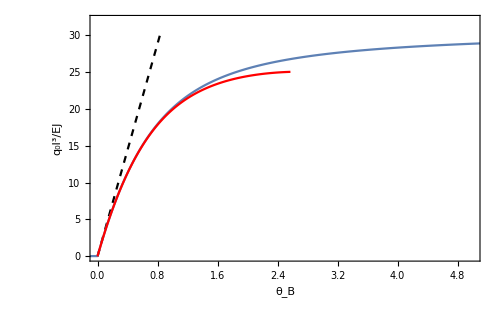

```mathematica
l=1.;
EJ=1.;

xin=0.01;
xfin=30.73;
ninterv=1000;

data0=Table[{θB[xin+(xfin-xin)/ninterv*i],xin+(xfin-xin)/ninterv*i},{i,0,ninterv}];
graph0=ListPlot[data0,Joined->True,PlotStyle->Directive[Black,Dashed]];


data1=Table[{θBnl[xin+(xfin-xin)/ninterv*i],xin+(xfin-xin)/ninterv*i},{i,0,ninterv}];
graph1=ListPlot[data1,Joined->True];

data2=res;
graph2=ListPlot[res,Joined->True,PlotStyle->Directive[Red]];

Show[{graph0,graph1,graph2},
PlotRange->{{0,5},{0,32}},
AspectRatio->1/GoldenRatio,
FrameTicks->{{{0,5,10,15,20,25,30},None},{Automatic,None}},
PlotRangePadding->None,
PlotRangeClipping->True,
Axes->False,
Frame->True,
FrameLabel->{"θ_B","q_0l^3/EJ"},
LabelStyle->18,
ImageSize->500
]
```

#### Primo carico e modo critico (anti-simmetrico)

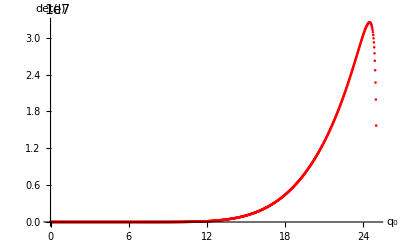

```mathematica
ListPlot[resdetJ, Joined->False, 
PlotStyle->Directive[Red], 
AxesLabel->{"q_0", "det(J)"}]
```

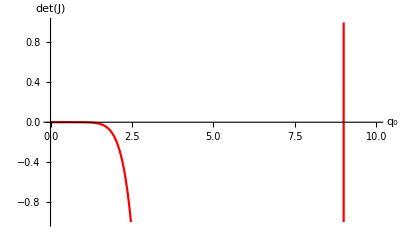

```mathematica
ListPlot[resdetJ,Joined->True,
PlotStyle->Directive[Red], 
AxesLabel->{"q_0", "det(J)"}, PlotRange->{{0,10}, {-1,1}}]
```

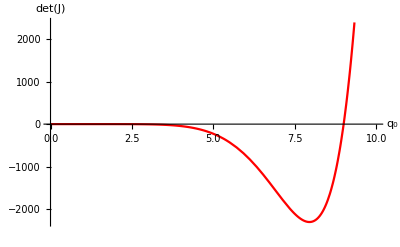

```mathematica
detJinterp = Interpolation[resdetJ];

Plot[detJinterp[q0], {q0, 0, 10}, PlotRange->{{0, 10}, Automatic}, PlotStyle->Directive[Red], AxesLabel->{"q_0", "det(J)"}]
```

```mathematica
q0cr = q0/.FindRoot[detJinterp[q0], {q0, 9}]
```

9.00193

#### Secondo carico e modo critico (simmetrico)

```mathematica
ListPlot[resdetJ, Joined->False, 
PlotStyle->Directive[Red], 
AxesLabel->{"q_0", "det(J)"}]
```

-Graphics-

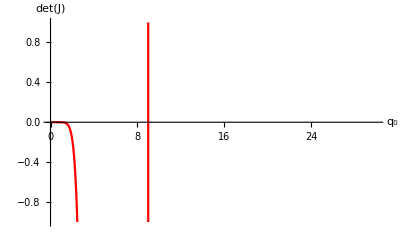

```mathematica
ListPlot[resdetJ,Joined->True,
PlotStyle->Directive[Red], 
AxesLabel->{"q_0", "det(J)"}, PlotRange->{{0,30}, {-1,1}}]
```

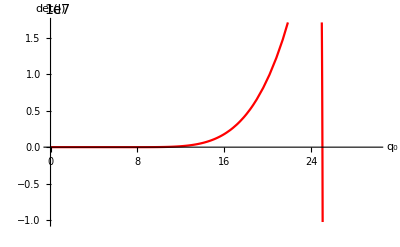

```mathematica
detJinterp = Interpolation[resdetJ];

Plot[detJinterp[q0], {q0, 0, 30}, PlotRange->{{0, 30}, Automatic}, PlotStyle->Directive[Red], AxesLabel->{"q_0", "det(J)"}]
```

```mathematica
q0cr = q0/.FindRoot[detJinterp[q0], {q0, 25}]
```

InterpolatingFunction::dmval: Input value {25.0754} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25.0534} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

25.0499

### Azioni assiali

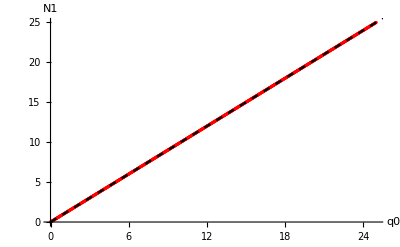

```mathematica
(* Azione assiale N1 *)
Show[{ListPlot[resN1,Joined->False,PlotStyle->Directive[Red]],Plot[N1lin[q0],{q0,0,30},PlotStyle->Directive[Black,Dashed]]},AxesLabel->{"q0","N1"}]
```

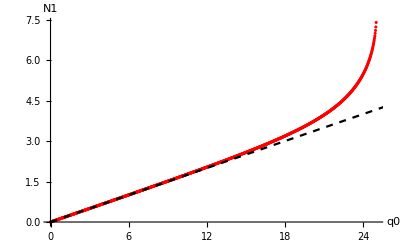

```mathematica
(* Azione assiale N2 *)
Show[{ListPlot[resN2,Joined->False,PlotStyle->Directive[Red]],Plot[N2lin[q0],{q0,0,30},PlotStyle->Directive[Black,Dashed]]},AxesLabel->{"q0","N1"}]
```

```mathematica
(* Azione assiale N3 *)
Show[{ListPlot[resN3,Joined->False,PlotStyle->Directive[Red]],Plot[N3lin[q0],{q0,0,30},PlotStyle->Directive[Black,Dashed]]},AxesLabel->{"q0","N1"}]
```

-Graphics-

## Soluzione con Abaqus in grandi spostamenti

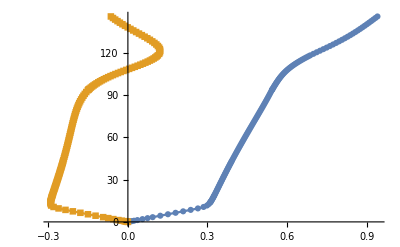

```mathematica
Ub23elasticamode1r =Import["G:\\Il mio Drive\\Jobs\\2020-2021\\Abaqus_Jobs\\Frame_Buckling\\Elastica\\Output\\Portal_U_mode_01_r_elastica.dat"];
Ub23elasticamode1l =Import["G:\\Il mio Drive\\Jobs\\2020-2021\\Abaqus_Jobs\\Frame_Buckling\\Elastica\\Output\\Portal_U_mode_01_l_elastica.dat"];
Ub23elasticamode1rn = Ub23elasticamode1r.DiagonalMatrix[{-1,9.0904}];
Ub23elasticamode1ln = Ub23elasticamode1l.DiagonalMatrix[{-1,9.0904}];

ListLinePlot[{Ub23elasticamode1rn,Ub23elasticamode1ln}, PlotMarkers->Automatic]
```